# Escape time versus initial shooting angle for some values of b

```mathematica
SetDirectory[NotebookDirectory[]];
```

Here we collect the plots in “EscapeTimeScatteringFunction.nb”

```mathematica
l[b_]:=If[$IsPositive,-3b+√(3+144 b^2),-3b-√(3+144 b^2)];
εcrit[b_]:=√(1+4 b Abs[l[b]]);
```

## Positive l (ε=1.2)

```mathematica
dataPts1=Import["pl_b(01)_e(12)_1.mx"];dataPts2=Import["pl_b(05)_e(12)_1.mx"];
```

```mathematica
plot=ListPlot[{dataPts1,dataPts2},PlotRange->{All,{0,10000}},PlotStyle-> {{Blue,PointSize[Medium]},{Red,PointSize[Medium]}},AxesLabel->{"ϕ_sh","T_e"},PlotLegends->Placed[LineLegend[{Blue,Red},{"b=0.1","b=0.5"},Joined->{True,True},LegendMarkerSize->80],{Right,Top}]];
```

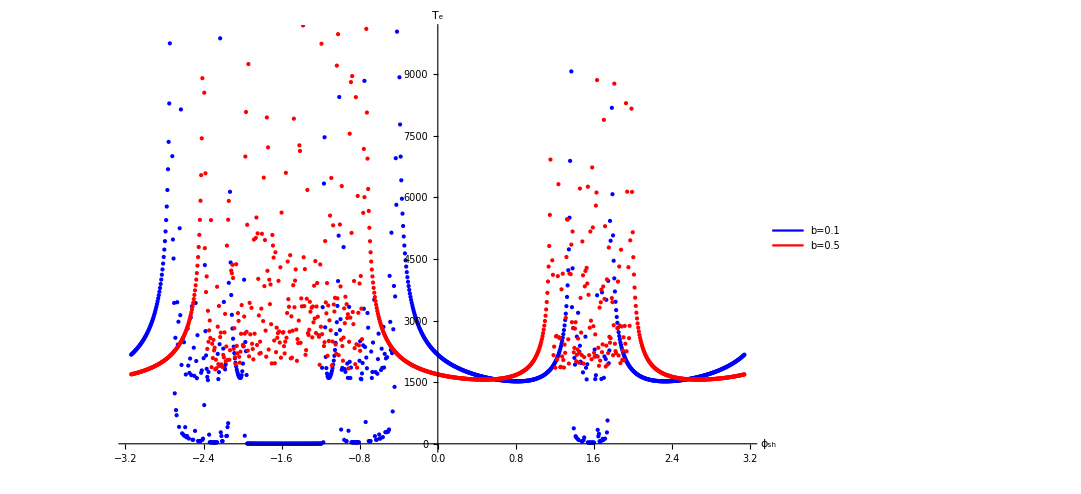

```mathematica
Show[plot,ImageSize->800]
```

```mathematica
Export["plNearCritE.png",Show[plot,ImageSize->2000,BaseStyle->{FontSize->40},LabelStyle->{FontSize->40}]]
```

plNearCritE.png

### b=0.1 zooms

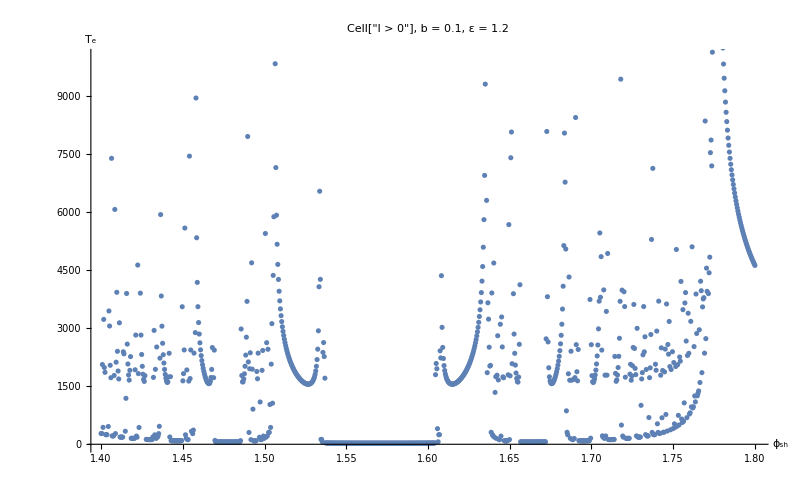

pl_b(01)_e(12)_2.png

```mathematica
dataPts=Import["pl_b(01)_e(12)_2.mx"];
plot=ListPlot[dataPts,PlotRange->{All,{0,10000}},PlotLabel->StringJoin["Cell["l > 0",ExpressionUUID->"45050c7c-1b25-4ce3-8768-4f26e6564a07"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"}];
Show[plot,LabelStyle->{FontSize->12},ImageSize->800]
Export["pl_b(01)_e(12)_2.png",Show[plot,LabelStyle->{FontSize->40},ImageSize->2000]]
```

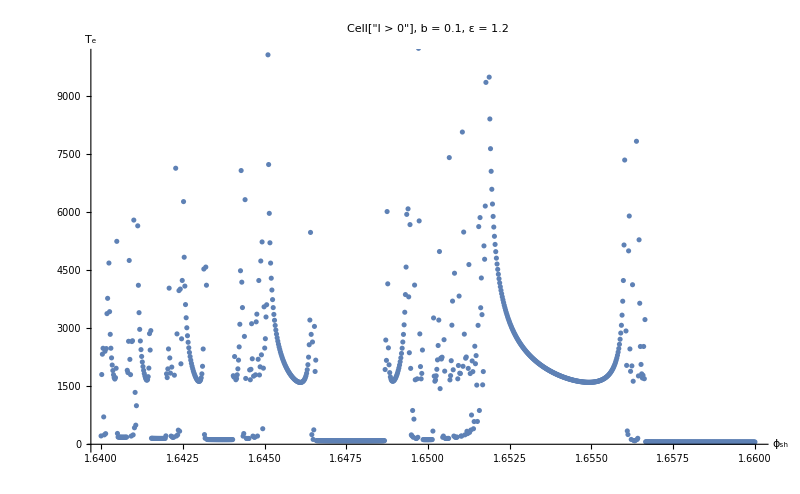

pl_b(01)_e(12)_3.png

```mathematica
dataPts=Import["pl_b(01)_e(12)_3.mx"];
plot=ListPlot[dataPts,PlotRange->{All,{0,10000}},PlotLabel->StringJoin["Cell["l > 0",ExpressionUUID->"2a8a9b7e-4ad0-472e-8b70-fd5a78a134fd"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"}];
Show[plot,LabelStyle->{FontSize->12},ImageSize->800]
Export["pl_b(01)_e(12)_3.png",Show[plot,LabelStyle->{FontSize->40},ImageSize->2000]]
```

### b=0.5 zooms

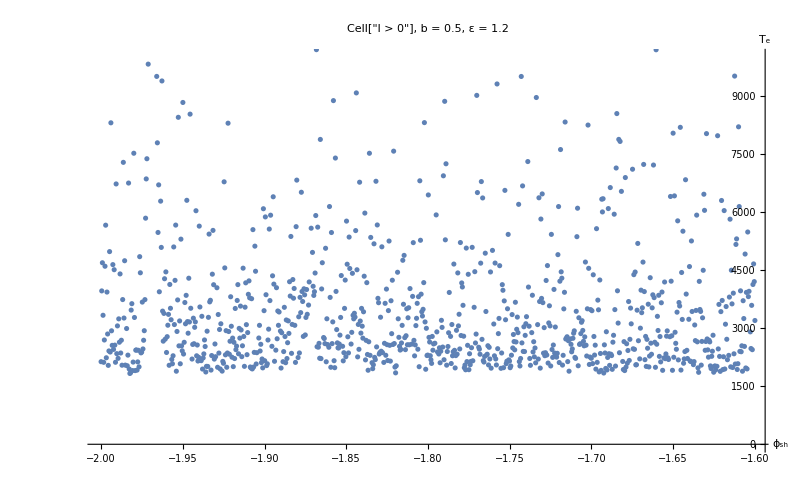

pl_b(05)_e(12)_2.png

```mathematica
dataPts=Import["pl_b(05)_e(12)_2.mx"];
plot=ListPlot[dataPts,PlotRange->{All,{0,10000}},PlotLabel->StringJoin["Cell["l > 0",ExpressionUUID->"a91dfcf8-45a9-483b-b61a-be258e1f2674"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"}];
Show[plot,LabelStyle->{FontSize->12},ImageSize->800]
Export["pl_b(05)_e(12)_2.png",Show[plot,LabelStyle->{FontSize->40},ImageSize->2000]]
```

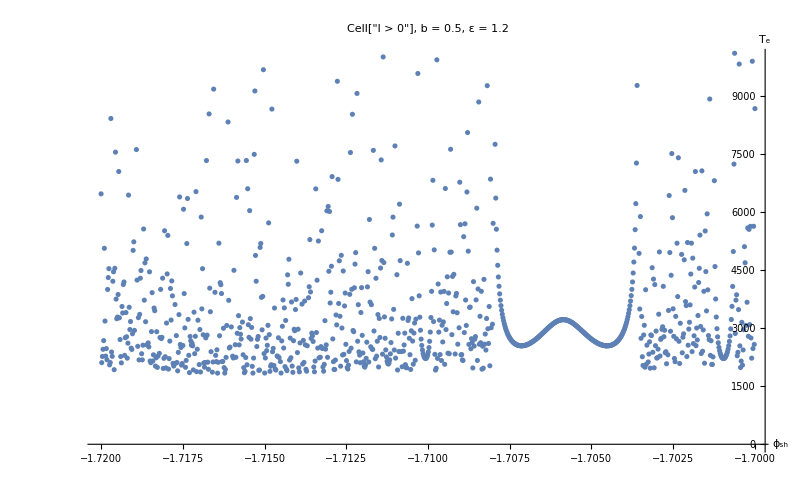

pl_b(05)_e(12)_3.png

```mathematica
dataPts=Import["pl_b(05)_e(12)_3.mx"];
plot=ListPlot[dataPts,PlotRange->{All,{0,10000}},PlotLabel->StringJoin["Cell["l > 0",ExpressionUUID->"9385dab4-bb25-494a-b81d-eeeb30192433"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"}];
Show[plot,LabelStyle->{FontSize->12},ImageSize->800]
Export["pl_b(05)_e(12)_3.png",Show[plot,LabelStyle->{FontSize->40},ImageSize->2000]]
```

## Positive l (ε=3.0)

```mathematica
dataPts1=Import["pl_b(01)_e(30)_1.mx"];dataPts2=Import["pl_b(05)_e(30)_1.mx"];
```

```mathematica
plot=ListPlot[{dataPts1,dataPts2},PlotRange->{All,{0,6000}},PlotStyle-> {{Blue,PointSize[Medium]},{Red,PointSize[Medium]}},AxesLabel->{"ϕ_sh","T_e"},PlotLegends->Placed[LineLegend[{Blue,Red},{"b=0.1","b=0.5"},Joined->{True,True},LegendMarkerSize->80],{Right,Top}]];
```

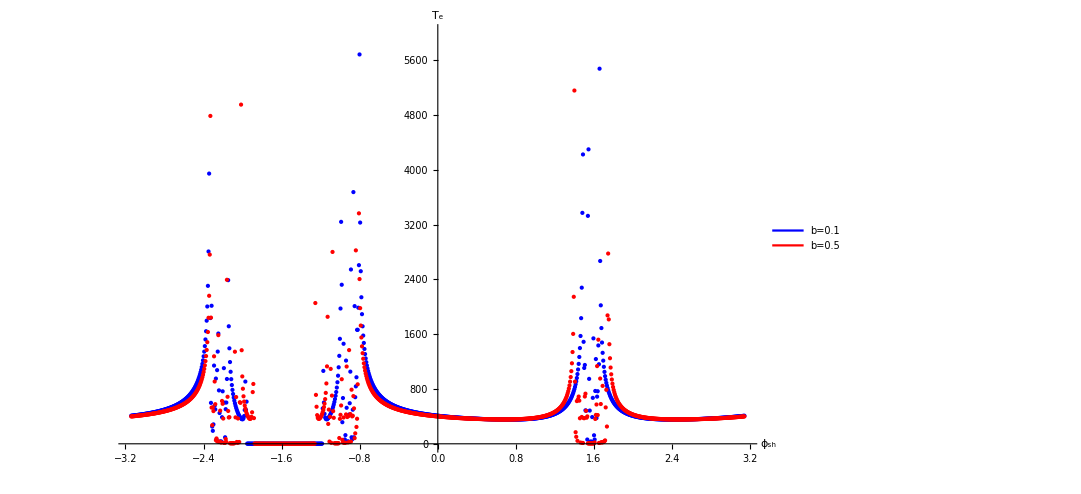

```mathematica
Show[plot,ImageSize->800]
```

```mathematica
Export["plFarCritE.png",Show[plot,ImageSize->2000,BaseStyle->{FontSize->40},LabelStyle->{FontSize->40}]]
```

plFarCritE.png

### b=0.1 zooms

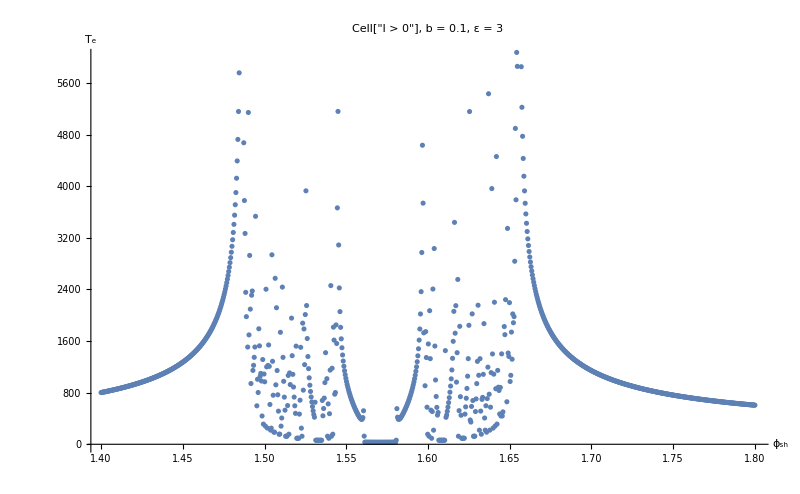

pl_b(01)_e(30)_2.png

```mathematica
dataPts=Import["pl_b(01)_e(30)_2.mx"];
plot=ListPlot[dataPts,PlotRange->{All,{0,6000}},PlotLabel->StringJoin["Cell["l > 0",ExpressionUUID->"33638817-cca2-4e3b-9b32-960e9191837b"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"}];
Show[plot,LabelStyle->{FontSize->12},ImageSize->800]
Export["pl_b(01)_e(30)_2.png",Show[plot,LabelStyle->{FontSize->40},ImageSize->2000]]
```

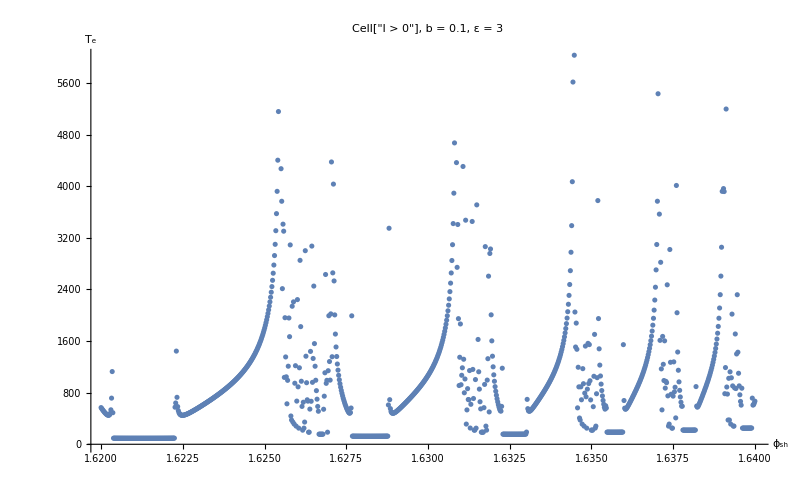

pl_b(01)_e(30)_3.png

```mathematica
dataPts=Import["pl_b(01)_e(30)_3.mx"];
plot=ListPlot[dataPts,PlotRange->{All,{0,6000}},PlotLabel->StringJoin["Cell["l > 0",ExpressionUUID->"78a7c347-7ef1-44fc-9a4d-36cd52bb29ab"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"}];
Show[plot,LabelStyle->{FontSize->12},ImageSize->800]
Export["pl_b(01)_e(30)_3.png",Show[plot,LabelStyle->{FontSize->40},ImageSize->2000]]
```

### b=0.5 zooms

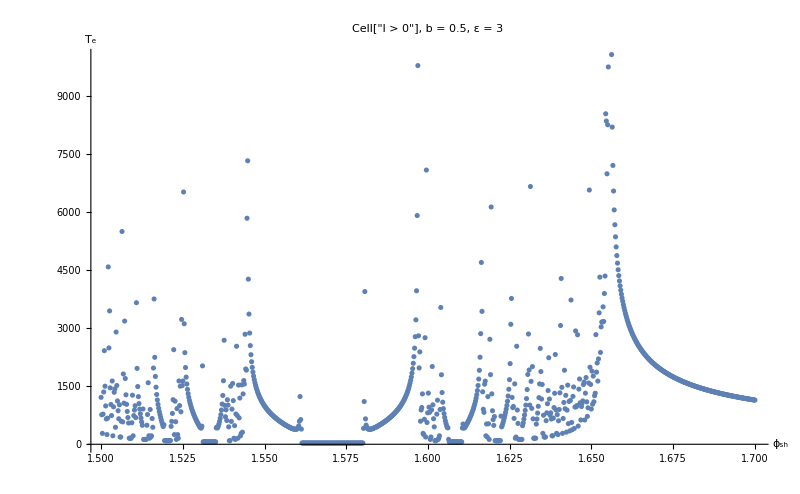

pl_b(05)_e(30)_2.png

```mathematica
dataPts=Import["pl_b(05)_e(30)_2.mx"];
plot=ListPlot[dataPts,PlotRange->{All,{0,10000}},PlotLabel->StringJoin["Cell["l > 0",ExpressionUUID->"61d3fbc9-55de-4071-8f19-684d9e728d12"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"}];
Show[plot,LabelStyle->{FontSize->12},ImageSize->800]
Export["pl_b(05)_e(30)_2.png",Show[plot,LabelStyle->{FontSize->40},ImageSize->2000]]
```

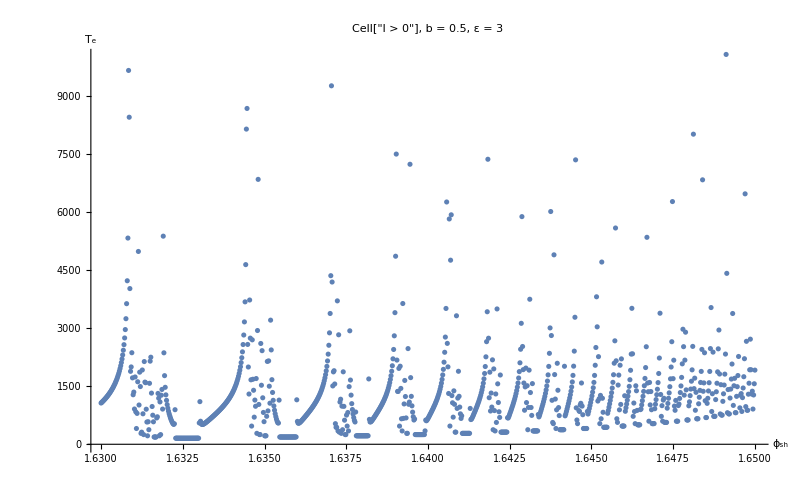

pl_b(05)_e(30)_3.png

```mathematica
dataPts=Import["pl_b(05)_e(30)_3.mx"];
plot=ListPlot[dataPts,PlotRange->{All,{0,10000}},PlotLabel->StringJoin["Cell["l > 0",ExpressionUUID->"91dde60d-7af8-4e8e-9514-a492657f23e7"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"}];
Show[plot,LabelStyle->{FontSize->12},ImageSize->800]
Export["pl_b(05)_e(30)_3.png",Show[plot,LabelStyle->{FontSize->40},ImageSize->2000]]
```

## Negative l (ε=ε_crit+0.2)

```mathematica
$IsPositive=False;
```

```mathematica
dataPts1=Import["ml_b(001)_e(ecrit_02)_1.mx"];dataPts2=Import["ml_b(01)_e(ecrit_02)_1.mx"];dataPts3=Import["ml_b(05)_e(ecrit_02)_1.mx"];
```

```mathematica
plotwb001=ListPlot[{dataPts1,dataPts2,dataPts3},PlotRange->{All,{0,10000}},PlotStyle-> {{Green,PointSize[Medium]},{Blue,PointSize[Medium]},{Red,PointSize[Medium]}},AxesLabel->{"ϕ_sh","T_e"},PlotLegends->Placed[LineLegend[{Green,Blue,Red},{"b=0.01 (ε="<>ToString[N[εcrit[0.01]+0.2,3]]<>")","b=0.1 (ε="<>ToString[N[εcrit[0.1]+0.2,3]]<>")","b=0.5 (ε="<>ToString[N[εcrit[0.5]+0.2,3]]<>")"},Joined->{True,True},LegendMarkerSize->80],{Right,Top}]];
plotwob001=ListPlot[{dataPts2,dataPts3},PlotRange->{All,{0,10000}},PlotStyle-> {{Blue,PointSize[Medium]},{Red,PointSize[Medium]}},AxesLabel->{"ϕ_sh","T_e"},PlotLegends->Placed[LineLegend[{Blue,Red},{"b=0.1 (ε="<>ToString[N[εcrit[0.1]+0.2,3]]<>")","b=0.5 (ε="<>ToString[N[εcrit[0.5]+0.2,3]]<>")"},Joined->{True,True},LegendMarkerSize->80],{Right,Top}]];
```

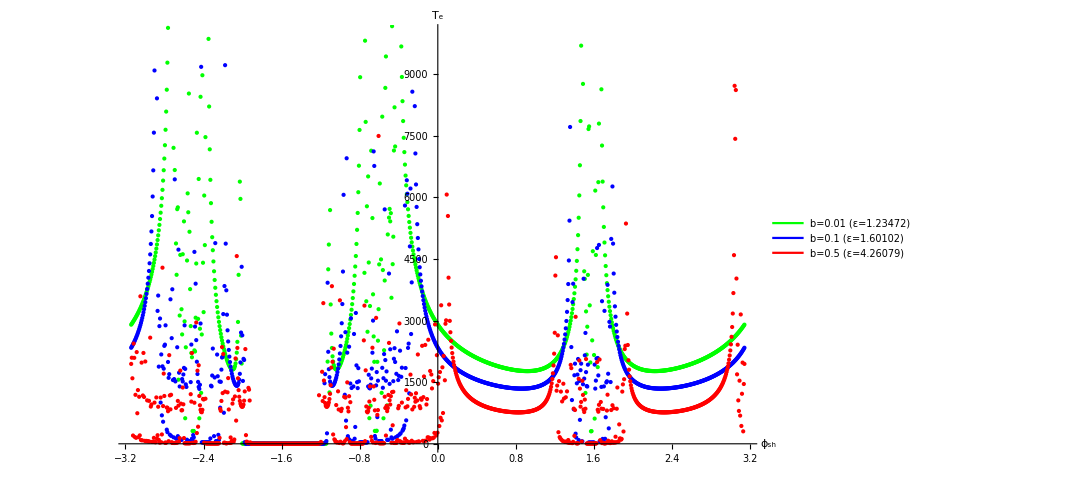

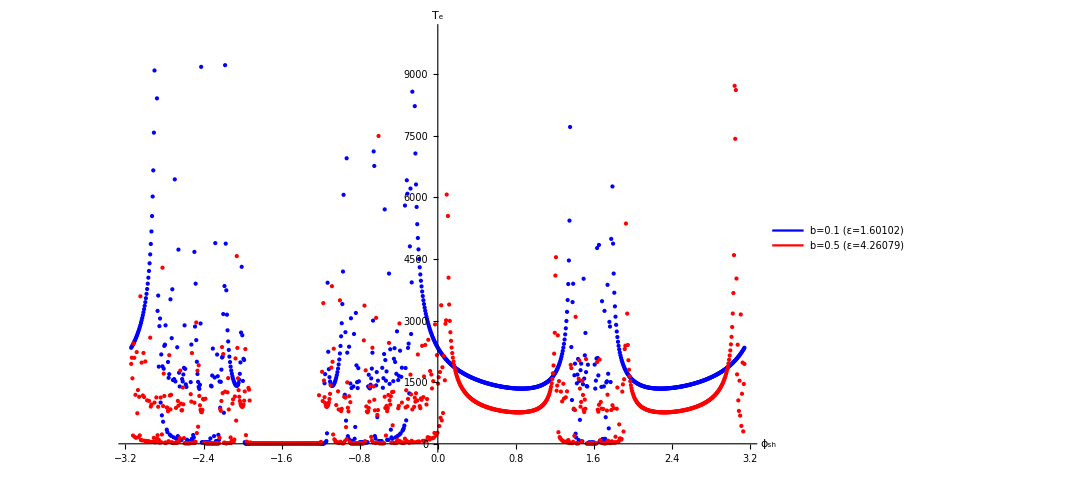

```mathematica
Show[plotwb001,ImageSize->800]
Show[plotwob001,ImageSize->800]
```

```mathematica
Export["mlNearCritE(wb001).png",Show[plotwb001,ImageSize->2000,BaseStyle->{FontSize->40},LabelStyle->{FontSize->40}]]
Export["mlNearCritE(wob001).png",Show[plotwob001,ImageSize->2000,BaseStyle->{FontSize->40},LabelStyle->{FontSize->40}]]
```

mlNearCritE(wb001).png

mlNearCritE(wob001).png

### b=0.01 zooms

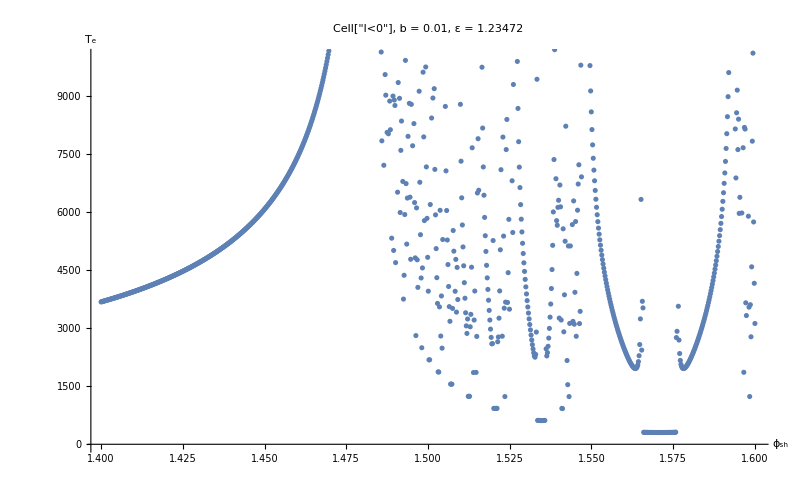

ml_b(001)_e(ecrit_02)_2.png

```mathematica
dataPts=Import["ml_b(001)_e(ecrit_02)_2.mx"];
plot=ListPlot[dataPts,PlotRange->{All,{0,10000}},PlotLabel->StringJoin["Cell["l<0",ExpressionUUID->"f307cd19-bd48-4a7f-b692-72785178a3dd"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"}];
Show[plot,LabelStyle->{FontSize->12},ImageSize->800]
Export["ml_b(001)_e(ecrit_02)_2.png",Show[plot,LabelStyle->{FontSize->40},ImageSize->2000]]
```

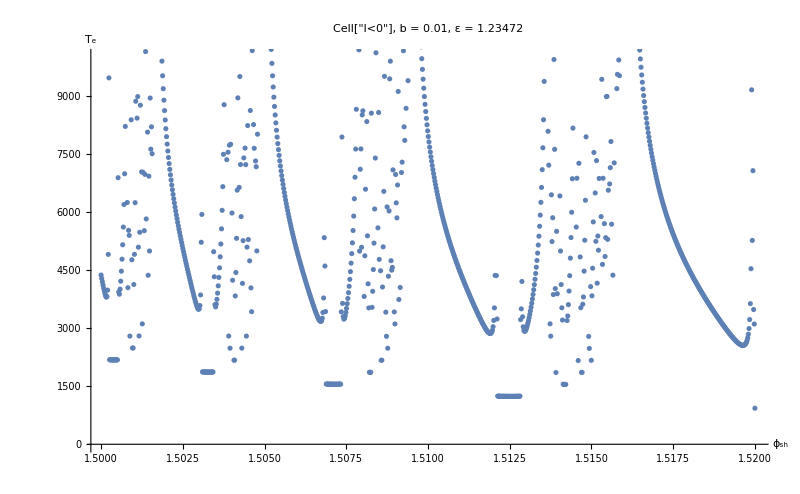

ml_b(001)_e(ecrit_02)_3.png

```mathematica
dataPts=Import["ml_b(001)_e(ecrit_02)_3.mx"];
plot=ListPlot[dataPts,PlotRange->{All,{0,10000}},PlotLabel->StringJoin["Cell["l<0",ExpressionUUID->"f7c09ff4-bc50-47a1-9c12-9505bb7173c1"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"}];
Show[plot,LabelStyle->{FontSize->12},ImageSize->800]
Export["ml_b(001)_e(ecrit_02)_3.png",Show[plot,LabelStyle->{FontSize->40},ImageSize->2000]]
```

### b=0.1 zooms

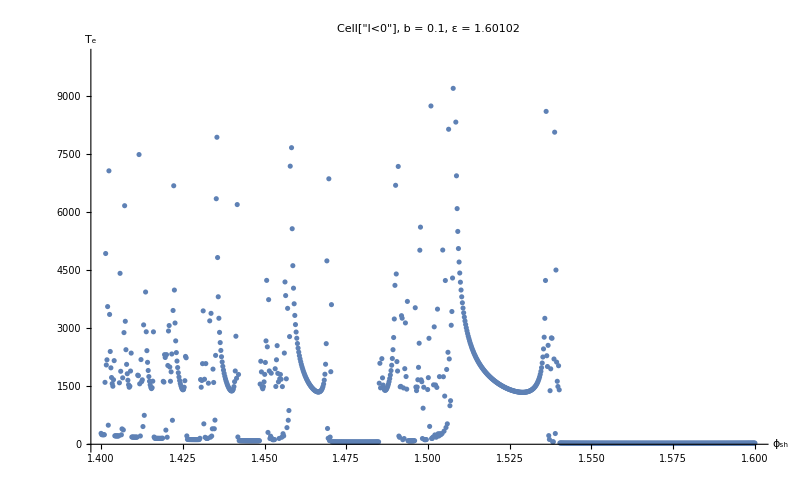

ml_b(01)_e(ecrit_02)_2.png

```mathematica
dataPts=Import["ml_b(01)_e(ecrit_02)_2.mx"];
plot=ListPlot[dataPts,PlotRange->{All,{0,10000}},PlotLabel->StringJoin["Cell["l<0",ExpressionUUID->"f0a7b2a1-cf51-4cbf-afe8-6f214a413c8c"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"}];
Show[plot,LabelStyle->{FontSize->12},ImageSize->800]
Export["ml_b(01)_e(ecrit_02)_2.png",Show[plot,LabelStyle->{FontSize->40},ImageSize->2000]]
```

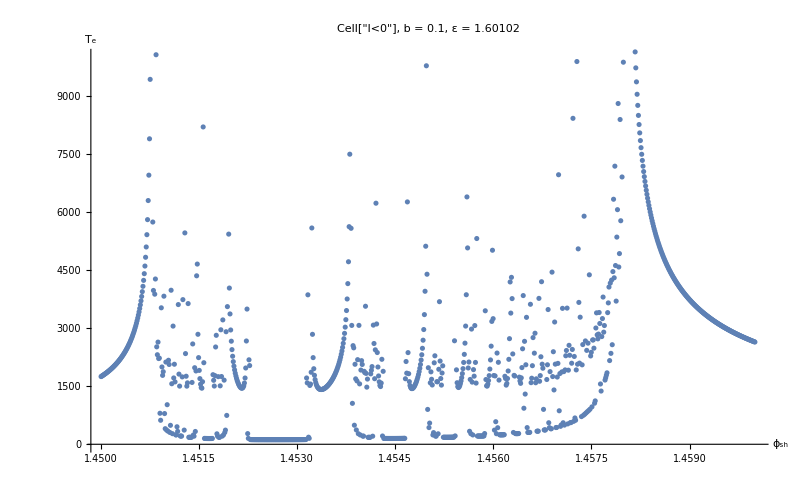

ml_b(01)_e(ecrit_02)_3.png

```mathematica
dataPts=Import["ml_b(01)_e(ecrit_02)_3.mx"];
plot=ListPlot[dataPts,PlotRange->{All,{0,10000}},PlotLabel->StringJoin["Cell["l<0",ExpressionUUID->"33503b3c-17fd-4e1d-9dfa-171aae1cdf33"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"}];
Show[plot,LabelStyle->{FontSize->12},ImageSize->800]
Export["ml_b(01)_e(ecrit_02)_3.png",Show[plot,LabelStyle->{FontSize->40},ImageSize->2000]]
```

### b=0.5 zooms

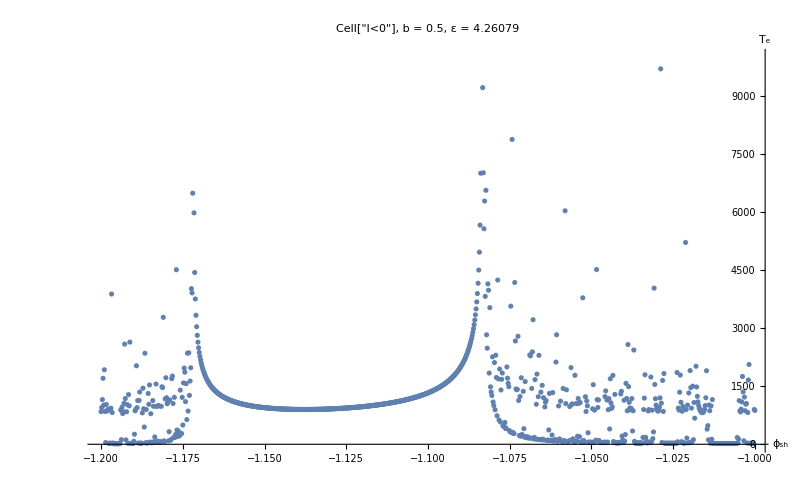

ml_b(05)_e(ecrit_02)_2.png

```mathematica
dataPts=Import["ml_b(05)_e(ecrit_02)_2.mx"];
plot=ListPlot[dataPts,PlotRange->{All,{0,10000}},PlotLabel->StringJoin["Cell["l<0",ExpressionUUID->"e15181c1-0153-46be-853d-ba247eb4ea1c"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"}];
Show[plot,LabelStyle->{FontSize->12},ImageSize->800]
Export["ml_b(05)_e(ecrit_02)_2.png",Show[plot,LabelStyle->{FontSize->40},ImageSize->2000]]
```

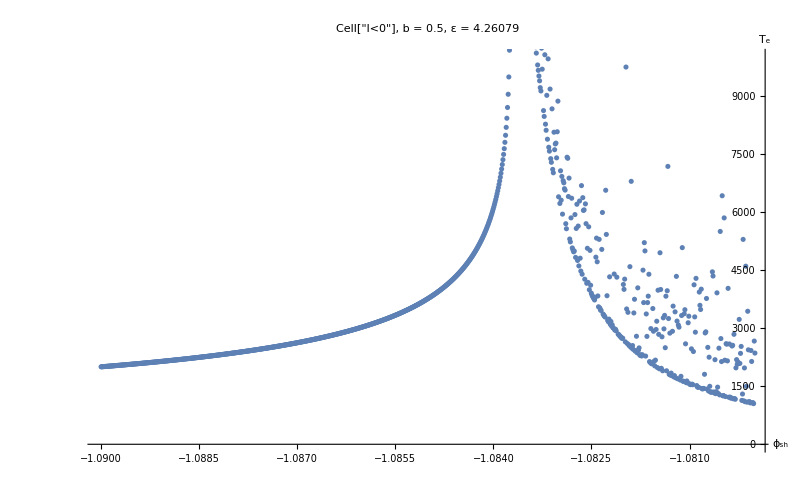

ml_b(05)_e(ecrit_02)_3.png

```mathematica
dataPts=Import["ml_b(05)_e(ecrit_02)_3.mx"];
plot=ListPlot[dataPts,PlotRange->{All,{0,10000}},PlotLabel->StringJoin["Cell["l<0",ExpressionUUID->"87185cfa-7739-4d38-beb1-5aa56f9c7ef5"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"}];
Show[plot,LabelStyle->{FontSize->12},ImageSize->800]
Export["ml_b(05)_e(ecrit_02)_3.png",Show[plot,LabelStyle->{FontSize->40},ImageSize->2000]]
```

## Negative l (ε=ε_crit+2)

```mathematica
dataPts1=Import["ml_b(001)_e(ecrit_2)_1.mx"];dataPts2=Import["ml_b(01)_e(ecrit_2)_1.mx"];dataPts3=Import["ml_b(05)_e(ecrit_2)_1.mx"];
```

```mathematica
plotwb001=ListPlot[{dataPts1,dataPts2,dataPts3},PlotRange->{All,{0,10000}},PlotStyle-> {{Green,PointSize[Medium]},{Blue,PointSize[Medium]},{Red,PointSize[Medium]}},AxesLabel->{"ϕ_sh","T_e"},PlotLegends->Placed[LineLegend[{Green,Blue,Red},{"b=0.01 (ε="<>ToString[N[εcrit[0.01]+2,3]]<>")","b=0.1 (ε="<>ToString[N[εcrit[0.1]+2,3]]<>")","b=0.5 (ε="<>ToString[N[εcrit[0.5]+2,3]]<>")"},Joined->{True,True},LegendMarkerSize->80],{Right,Top}]];
plotwob001=ListPlot[{dataPts2,dataPts3},PlotRange->{All,{0,10000}},PlotStyle-> {{Blue,PointSize[Medium]},{Red,PointSize[Medium]}},AxesLabel->{"ϕ_sh","T_e"},PlotLegends->Placed[LineLegend[{Blue,Red},{"b=0.1 (ε="<>ToString[N[εcrit[0.1]+2,3]]<>")","b=0.5 (ε="<>ToString[N[εcrit[0.5]+2,3]]<>")"},Joined->{True,True},LegendMarkerSize->80],{Right,Top}]];
```

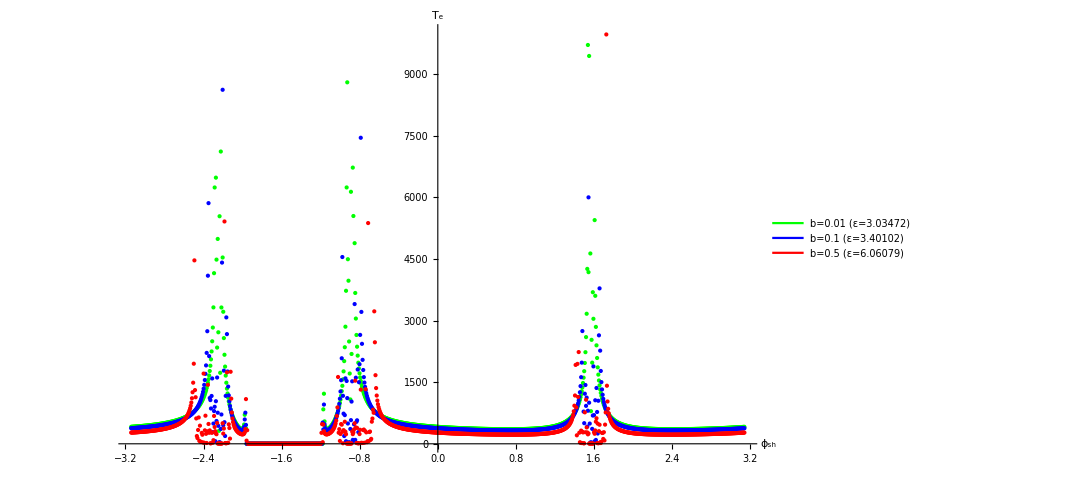

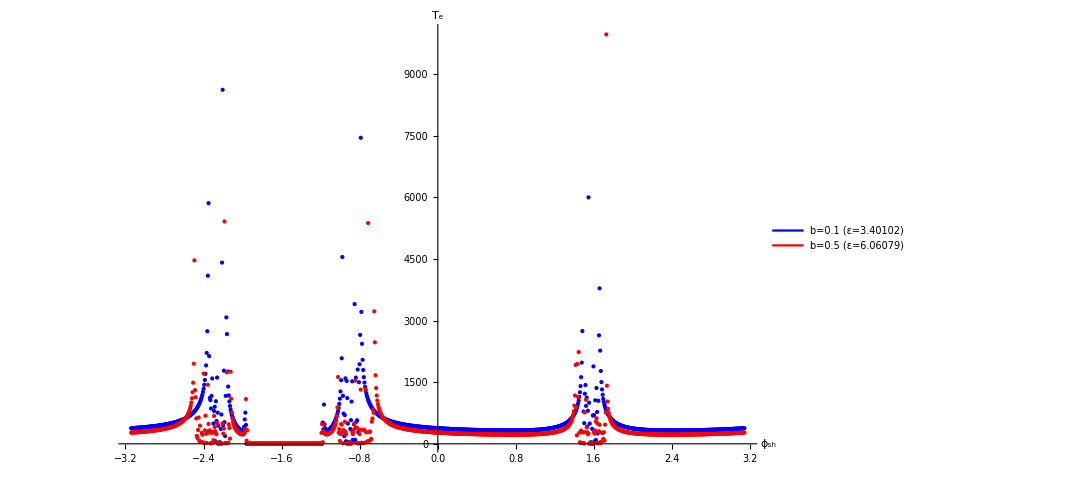

```mathematica
Show[plotwb001,ImageSize->800]
Show[plotwob001,ImageSize->800]
```

```mathematica
Export["mlFarCritE(wb001).png",Show[plotwb001,ImageSize->2000,BaseStyle->{FontSize->40},LabelStyle->{FontSize->40}]]
Export["mlFarCritE(wob001).png",Show[plotwob001,ImageSize->2000,BaseStyle->{FontSize->40},LabelStyle->{FontSize->40}]]
```

mlFarCritE(wb001).png

mlFarCritE(wob001).png

### b=0.01 zooms

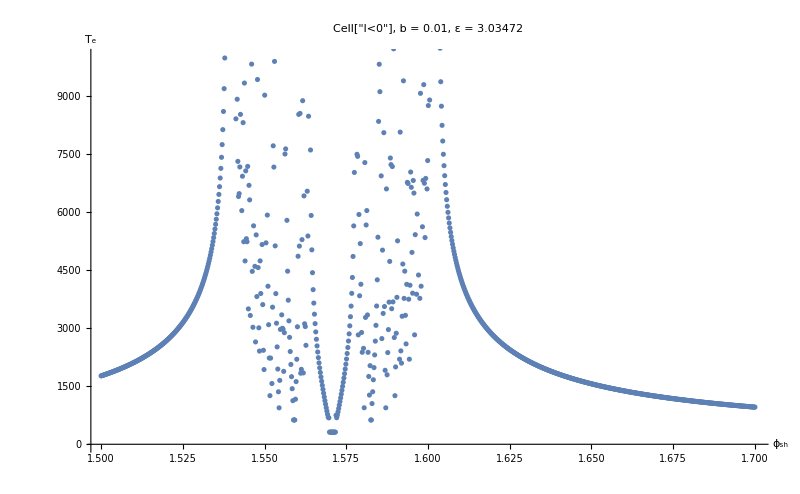

ml_b(001)_e(ecrit_2)_2.png

```mathematica
dataPts=Import["ml_b(001)_e(ecrit_2)_2.mx"];
plot=ListPlot[dataPts,PlotRange->{All,{0,10000}},PlotLabel->StringJoin["Cell["l<0",ExpressionUUID->"b6859580-eea7-4f7d-821a-2a607309a71d"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"}];
Show[plot,LabelStyle->{FontSize->12},ImageSize->800]
Export["ml_b(001)_e(ecrit_2)_2.png",Show[plot,LabelStyle->{FontSize->40},ImageSize->2000]]
```

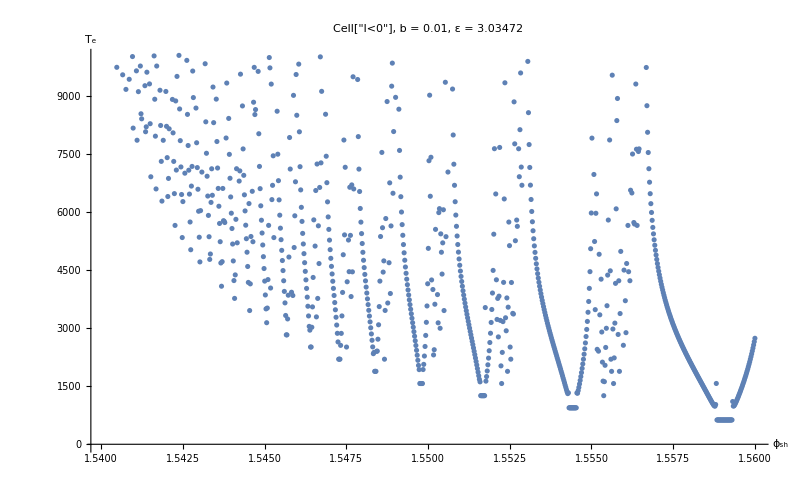

ml_b(001)_e(ecrit_2)_3.png

```mathematica
dataPts=Import["ml_b(001)_e(ecrit_2)_3.mx"];
plot=ListPlot[dataPts,PlotRange->{All,{0,10000}},PlotLabel->StringJoin["Cell["l<0",ExpressionUUID->"b81e3e41-4022-48b9-9245-a15fcab68148"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"}];
Show[plot,LabelStyle->{FontSize->12},ImageSize->800]
Export["ml_b(001)_e(ecrit_2)_3.png",Show[plot,LabelStyle->{FontSize->40},ImageSize->2000]]
```

### b=0.1 zooms

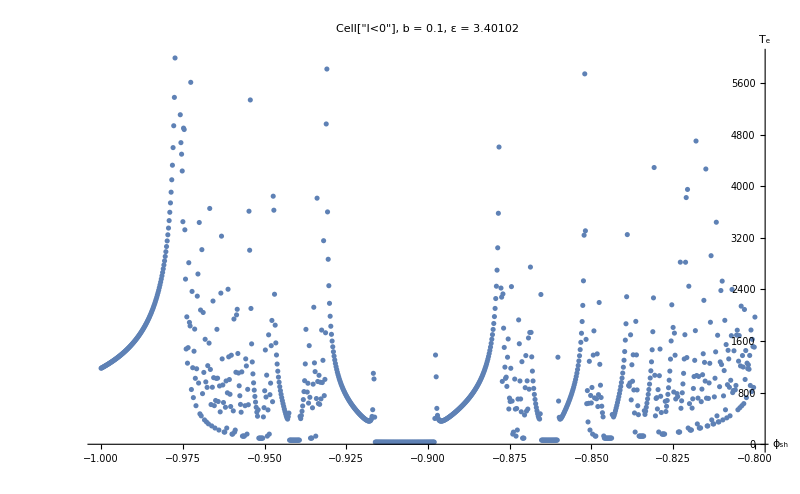

ml_b(01)_e(ecrit_2)_2.png

```mathematica
dataPts=Import["ml_b(01)_e(ecrit_2)_2.mx"];
plot=ListPlot[dataPts,PlotRange->{All,{0,6000}},PlotLabel->StringJoin["Cell["l<0",ExpressionUUID->"c76255b3-d5fc-4f1f-bc41-a08051a5a002"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"}];
Show[plot,LabelStyle->{FontSize->12},ImageSize->800]
Export["ml_b(01)_e(ecrit_2)_2.png",Show[plot,LabelStyle->{FontSize->40},ImageSize->2000]]
```

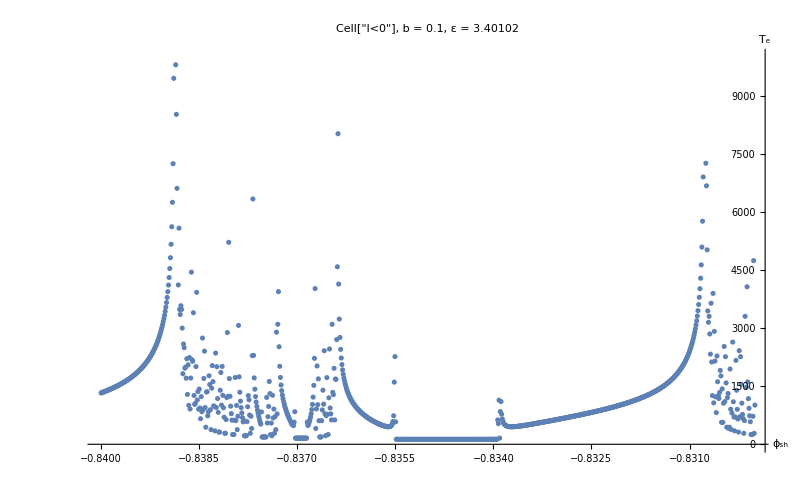

ml_b(01)_e(ecrit_2)_3.png

```mathematica
dataPts=Import["ml_b(01)_e(ecrit_2)_3.mx"];
plot=ListPlot[dataPts,PlotRange->{All,{0,10000}},PlotLabel->StringJoin["Cell["l<0",ExpressionUUID->"7c95eba2-3cdf-4d38-b267-1a13774c8f32"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"}];
Show[plot,LabelStyle->{FontSize->12},ImageSize->800]
Export["ml_b(01)_e(ecrit_2)_3.png",Show[plot,LabelStyle->{FontSize->40},ImageSize->2000]]
```

## b=0.5 zooms

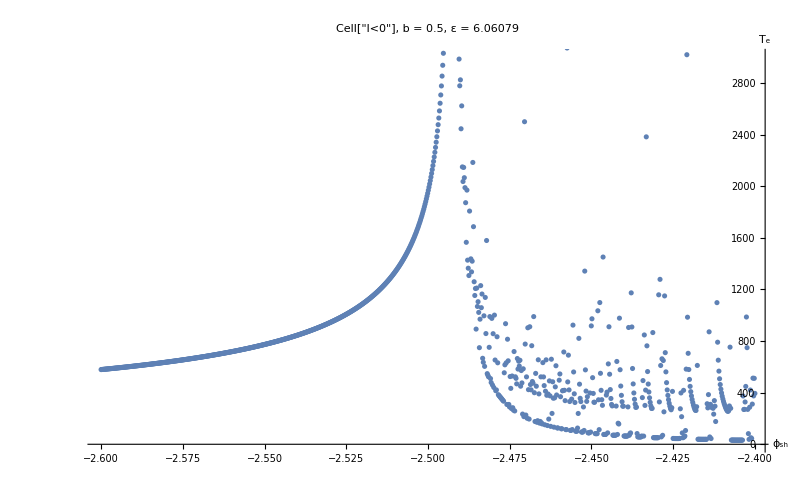

ml_b(05)_e(ecrit_2)_2.png

```mathematica
dataPts=Import["ml_b(05)_e(ecrit_2)_2.mx"];
plot=ListPlot[dataPts,PlotRange->{All,{0,3000}},PlotLabel->StringJoin["Cell["l<0",ExpressionUUID->"dd5ebda8-30d0-423f-84cc-a5ea5cd30db2"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"}];
Show[plot,LabelStyle->{FontSize->12},ImageSize->800]
Export["ml_b(05)_e(ecrit_2)_2.png",Show[plot,LabelStyle->{FontSize->40},ImageSize->2000]]
```

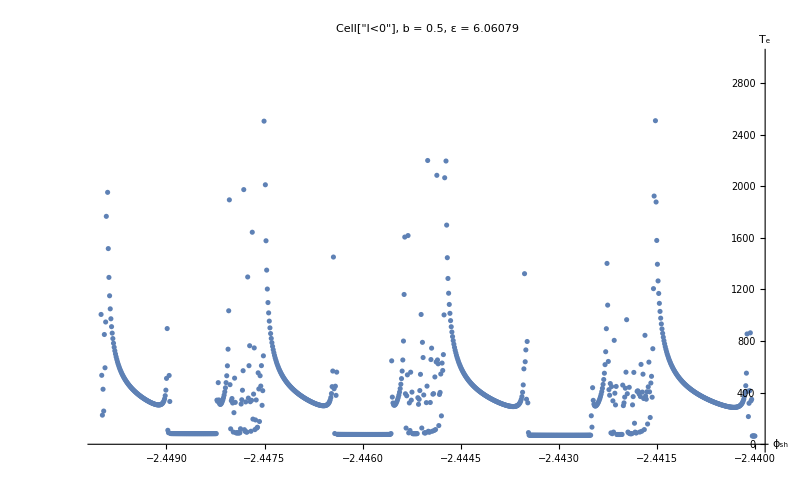

ml_b(05)_e(ecrit_2)_3.png

```mathematica
dataPts=Import["ml_b(05)_e(ecrit_2)_3.mx"];
plot=ListPlot[dataPts,PlotRange->{All,{0,3000}},PlotLabel->StringJoin["Cell["l<0",ExpressionUUID->"e79a13d9-a61c-4767-9d16-a1e0113fd6b0"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"}];
Show[plot,LabelStyle->{FontSize->12},ImageSize->800]
Export["ml_b(05)_e(ecrit_2)_3.png",Show[plot,LabelStyle->{FontSize->40},ImageSize->2000]]
```